C d (C (p+ı q)+a X-b ı Y) ℑ==d q X^2+d (a+p) X Y+d (-b+p) X Y-d q Y^2==0

```mathematica
EC = ComplexExpand[(((p + I q)(X + I Y) + a X - I b Y))(X'+ I Y')]
```

a X X'+p X X'-q Y X'-q X Y'+b Y Y'-p Y Y'+ⅈ (q X X'-b Y X'+p Y X'+a X Y'+p X Y'-q Y Y')

```mathematica
Eq = (EC - (EC/.I->-I))/(2 I)
```

q X X'-b Y X'+p Y X'+a X Y'+p X Y'-q Y Y'

```mathematica
Eq1 =((Eq/.{X'-> D[E^f[θ]Cos[θ],θ], Y'->D[E^f[θ]Sin[θ],θ],X ->E^f[θ]Cos[θ],Y ->E^f[θ]Sin[θ]})/E^(2f[θ]))//Simplify
```

1/2 (a+b+(a-b+2 p) Cos[2 θ]-2 q Sin[2 θ]+(2 q Cos[2 θ]+(a-b+2 p) Sin[2 θ]) f'[θ])

```mathematica
lr = (f[θ]/.DSolve[Eq1==0,f[θ],θ][[1]])/.{C[1]->0}
```

-(2 (a+b) ArcTanh[(-a+b-2 p+2 q Tan[θ])/(√(a^2-2 a b+b^2+4 a p-4 b p+4 p^2+4 q^2))]+√(a^2-2 a b+b^2+4 a p-4 b p+4 p^2+4 q^2) Log[2 q Cos[2 θ]+(a-b+2 p) Sin[2 θ]])/(2 √(a^2+b^2-2 a (b-2 p)-4 b p+4 (p^2+q^2)))

```mathematica
Sub[γ_, β_,a_,c_] :=
{
H ->  -c/(2γ+1 )Cos[2β],
q -> -c/(4γ+2) Sin[2β],
p ->(b - a - H)/2,
b -> - a-c
};
```

```mathematica
lfs=FullSimplify[lr//.Sub[γ,β, a,c],{c>0} ]
```

-((1+2 γ) ArcTanh[Cos[2 β-θ] Sec[θ]])-1/2 Log[-(c Sin[2 β-2 θ])/(1+2 γ)]

```mathematica
collectLog[expr_]:=Module[{rule1,rule2,rule3,a,b,x},
rule1=Log[a_]+Log[b_]:>Log[a*b];
rule2=x_*Log[a_]:>Log[a^x];
rule3 = x_ ArcTanh[a_] :> Log[(1 + a)^(x/2) (1-a)^(-x/2)];
expr//.{rule1,rule2,rule3}
];
```

```mathematica
r[θ_] :=FullSimplify[Sqrt[c/(2 γ +1)] Exp[collectLog[lfs]]/.Exp[Log[x_]] ->x,{c >0, γ>0}]
```

```mathematica
r[θ]
```

((Sec[θ] Sin[β] Sin[β-θ])^(1/2+γ) (Cos[β] (Cos[β]+Sin[β] Tan[θ]))^(-1/2-γ))/(√(-Sin[2 β-2 θ]))

```mathematica
CC =FullSimplify[((Sin[β] Sin[β-θ]))/(Cos[β] (Cos[β]Cos[θ]+Sin[β] Sin[θ])),{β,γ,θ} ∈ Reals]
```

Tan[β] Tan[β-θ]

```mathematica
r[θ_] := FullSimplify[CC^γ  Sqrt[ 2CC/Sin[2(β-θ)]]/.{Tan[β]->1,θ->β-θ},Sec[θ] >0]
```

```mathematica
r[θ]
```

Sec[θ] Tan[θ]^γ

```mathematica
(* switchingb to τ = Tan[θ] *)
```

```mathematica
FlameSub[τ_,γ_,β_]:= 
{η-> E^(I β)(τ^γ + I τ^(γ+1) ),
η*-> E^(-I β)(τ^γ - I τ^(γ+1) )};
```

```mathematica
A=FullSimplify[-(p+ 2a+c + I q )//.Sub[γ, β,a,c]]
```

-(c ⅇ^(-2 ⅈ β)+(2 a+c) (1+2 γ))/(2+4 γ)

```mathematica
F[τ_,γ_, β_] :=Simplify[Evaluate[FullSimplify[(A η + c η*)/.FlameSub[τ,γ,β],{γ,β,τ} ∈ Reals] ]]
```

```mathematica
F[τ,γ,β]
```

ⅇ^(-ⅈ β) τ^γ (c-ⅈ c τ-(ⅈ (c+(2 a+c) ⅇ^(2 ⅈ β) (1+2 γ)) (-ⅈ+τ))/(2+4 γ))

```mathematica
II = FullSimplify[D[(1 + I τ) τ^γ,τ]/(2 Pi I) F[τ,γ,β]/(η - (1 + I τ) τ^(α-1/2))]
```

(ⅇ^(-ⅈ β) τ^(2 γ) (τ+γ (-ⅈ+τ)) (c+4 c γ-ⅈ c (3+4 γ) τ-ⅈ (2 a+c) ⅇ^(2 ⅈ β) (1+2 γ) (-ⅈ+τ)))/(4 π (1+2 γ) (η τ-ⅈ τ^(1/2+α) (-ⅈ+τ)))

```mathematica
cp[τ_,γ_,β_] := D[Evaluate[η/.FlameSub[τ,γ,β]],τ]
```

```mathematica
FF[τ_,γ_,β_] := Simplify[Evaluate[FullSimplify[(cp[τ,γ,β]/(cp[τ,γ,β]/.τ->-τ))/.(-τ)^μ_ :> E^(I Pi μ) τ^μ,{γ,β,τ} ∈ Reals]]]
```

```mathematica
FF[τ,γ ,β]
```

(ⅇ^(-ⅈ π γ) (τ+γ (-ⅈ+τ)))/(τ+γ (ⅈ+τ))

```mathematica
FF[τ,γ,β]/.τ->0
```

-ⅇ^(-ⅈ π γ)

```mathematica
FullSimplify[FF[Tan[Pi/2γ],γ ,β],γ ∈ Reals]
```

(ⅇ^(-ⅈ π γ) (-ⅈ γ+(1+γ) Tan[(π γ)/2]))/(ⅈ γ+(1+γ) Tan[(π γ)/2])

```mathematica
-ExpToTrig[(γ+ I(1+γ) Tan[(π γ)/2])/(γ-I(1+γ) Tan[(π γ)/2])]
```

-(γ+ⅈ (1+γ) Tan[(π γ)/2])/(γ-ⅈ (1+γ) Tan[(π γ)/2])

```mathematica
DT2 =Pi(1-γ) + 2 ArcTan[(1+γ)/γ Tan[Pi γ/2]]
```

π (1-γ)+2 ArcTan[((1+γ) Tan[(π γ)/2])/γ]

```mathematica
Pi(1-γ)+ 2 ArcTan[((1+γ) Tan[(π γ)/2])/γ]
```

π (1-γ)+2 ArcTan[((1+γ) Tan[(π γ)/2])/γ]

```mathematica
DT1 = Pi(1-γ)
```

π (1-γ)

```mathematica
FlameSubPlus[τ_,γ_,β_]:= 
{η-> E^(I β)(τ^γ + I τ^(γ+1) ),
η*-> E^(-I β)(τ^γ - I τ^(γ+1) )
};
```

```mathematica
FlameSubMinus[τ_,γ_,β_]:= 
{η-> E^(I β) E^(I Pi γ)(τ^γ - I τ^(γ+1) ),
η*-> E^(-I β) E^(-I Pi γ)(τ^γ + I τ^(γ+1) ) };
```

```mathematica
A
```

-(c ⅇ^(-2 ⅈ β)+(2 a+c) (1+2 γ))/(2+4 γ)

```mathematica
ClearAll[α,β,γ]
α=Null;
```

```mathematica
FPlus[τ_,γ_, β_] := FullSimplify[(A η + c η*)/.FlameSubPlus[τ,γ,β],{γ,β,τ} ∈ Reals] ;
FMinus[τ_,γ_, β_] := FullSimplify[(A η + c η*)/.FlameSubMinus[τ,γ,β],{γ,β,τ} ∈ Reals];
```

```mathematica
FPlus[τ,γ, β]
```

ⅇ^(-ⅈ β) τ^γ (c-ⅈ c τ-(ⅈ (c+(2 a+c) ⅇ^(2 ⅈ β) (1+2 γ)) (-ⅈ+τ))/(2+4 γ))

```mathematica
FMinus[τ,γ, β]
```

-(ⅇ^(ⅈ (β+π γ)) (c ⅇ^(-2 ⅈ β)+(2 a+c) (1+2 γ)) (1-ⅈ τ) τ^γ)/(2+4 γ)+c ⅇ^(-ⅈ (β+π γ)) (1+ⅈ τ) τ^γ

```mathematica
CPPlus[τ_,γ_,β_] :=Evaluate[E^(I β)D[(1 + I τ) τ^γ,τ]]
```

```mathematica
CPPlus[τ,γ,β]
```

ⅇ^(ⅈ β) (γ (1+ⅈ τ) τ^(-1+γ)+ⅈ τ^γ)

```mathematica
CPMinus[τ_,γ_,β_] :=Simplify[ⅇ^(ⅈ β) ⅇ^(ⅈ π γ)(-γ (1-ⅈ τ) τ^(-1+γ)+ⅈ τ^γ)]
```

```mathematica
CPMinus[τ,γ,β]
```

ⅈ ⅇ^(ⅈ (β+π γ)) τ^(-1+γ) (τ+γ (ⅈ+τ))

```mathematica
IIPlus = FullSimplify[CPPlus[τ,γ,β]/(2 Pi I) FPlus[τ,γ,β]/(η - ⅇ^(ⅈ β)(1 + I τ) τ^γ)]
```

(τ^(-1+2 γ) (τ+γ (-ⅈ+τ)) ((2 a+c) ⅇ^(2 ⅈ β) (1+2 γ) (-ⅈ+τ)+c (ⅈ+3 τ+4 γ (ⅈ+τ))))/(4 π (1+2 γ) (ⅈ η+ⅇ^(ⅈ β) τ^γ (-ⅈ+τ)))

```mathematica
IIMinus = FullSimplify[CPMinus[τ,γ,β]/(2 Pi I) FMinus[τ,γ,β]/(η - ⅇ^(ⅈ β)ⅇ^(ⅈ π γ)(1 - I τ) τ^γ)]
```

(τ^(-1+2 γ) (τ+γ (ⅈ+τ)) (2 c (1+2 γ) (-ⅈ+τ)+ⅇ^(2 ⅈ π γ) (c+(2 a+c) ⅇ^(2 ⅈ β) (1+2 γ)) (ⅈ+τ)))/(4 π (1+2 γ) (-ⅈ η+ⅇ^(ⅈ (β+π γ)) τ^γ (ⅈ+τ)))

```mathematica
(*FullSimplify[IIPlus + IIMinus,{γ,β,a,c} ∈ Reals]*)
```

```mathematica
ClearAll[DeltaFPlus,DeltaFMinus];
```

```mathematica
DeltaFPlus[τ_,γ_,β_]:= FullSimplify[(-2(p + I q) η - a (η + η*) + b (η - η*))//.Sub[γ, β,a,c]/.FlameSubPlus[τ,γ,β]]
```

```mathematica
DeltaFMinus[τ_,γ_,β_]:= FullSimplify[(-2(p + I q) η - a (η + η*) + b (η - η*))//.Sub[γ,β,a,c]/.FlameSubMinus[τ,γ,β]]
```

```mathematica
DeltaGammaPlus =FullSimplify[ With[{x=Tan[Pi γ/2]},Integrate[CPPlus[τ,γ,β] DeltaFPlus[τ,γ,β],{τ,0,x},GenerateConditions->False]]]
```

(c Tan[(π γ)/2]^(2 γ) (γ+(1+γ) Tan[(π γ)/2]^2))/(1+2 γ)

```mathematica
DeltaGammaMinus = FullSimplify[With[{x=Tan[Pi γ/2]},Integrate[CPMinus[τ,γ,β] DeltaFMinus[τ,γ,β],{τ,0,x},GenerateConditions->False]]]
```

(c (-1-2 γ+Cos[π γ]+2 ⅈ Sin[π γ]) Tan[(π γ)/2]^(2 γ))/((1+2 γ) (1+Cos[π γ]))

```mathematica
FullSimplify[CPPlus[τ,γ,β]DeltaFPlus[τ,γ,β]]
```

(2 c τ^(-1+2 γ) (γ^2+(1+γ)^2 τ^2))/(1+2 γ)

```mathematica
Eq =FullSimplify[1/c Re[ DeltaGammaPlus + DeltaGammaMinus],{γ,β,a,c} ∈ Reals]
```

-2 Im[Tan[(π γ)/2]^(1+2 γ)/(1+2 γ)]

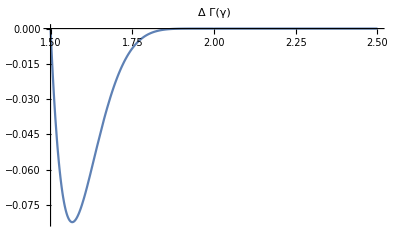

```mathematica
Plot[-2 Im[Tan[(π γ)/2]^(1+2 γ)/(1+2 γ)],{γ,1.5,2.5},PlotLabel->Δ Γ[γ]]
```

```mathematica
Wing[γ0_, β0_] := Block[{x},
x = Tan[Pi γ0/2];
ParametricPlot[ReIm[(1 + I τ) τ^γ0 Exp[I  β0]],{τ,-x,x},Exclusions->{x==0},  PlotLabel->{Symbol["γ"]==γ0,Symbol["β"]==β0},
MaxRecursion->8,
PlotRange->Full]]
```

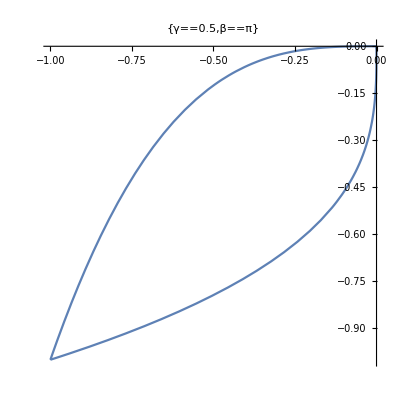

```mathematica
Wing[0.5,Pi]
```

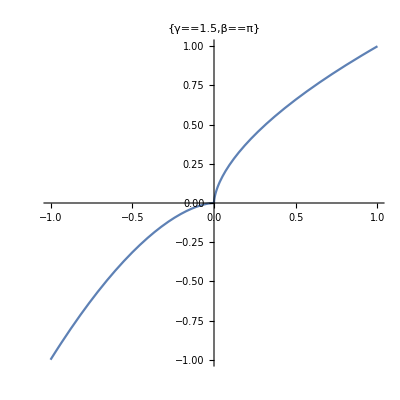

```mathematica
Wing[1.5,Pi]
```

```mathematica
"
```

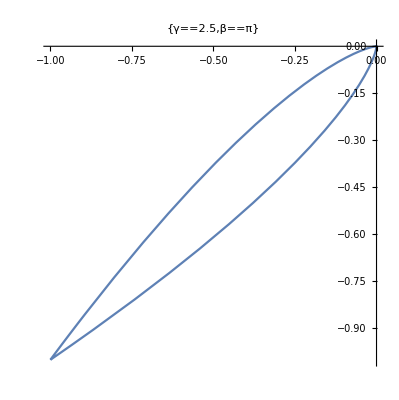

```mathematica
Wing[2.5,Pi]
```

```mathematica
GPMinus[γ_,τ_] := Evaluate[FullSimplify[(CPMinus[τ,γ,0] DeltaFMinus[τ,γ,0])/.{c->1}]];
GPPlus[γ_,τ_]   :=Evaluate[FullSimplify[(CPPlus[τ,γ,0] DeltaFPlus[τ,γ,0])/.{c->1}]];
```

```mathematica
CPlus[γ_,z_] := ( 1 + I z)z^γ;
CMinus[γ_,z_] :=  E^( I Pi γ)(1 -  I z)z^γ;
```

```mathematica
DeltaGamma[γ_] := Block[{ x = Tan[Pi γ/2]},FullSimplify[Integrate[GPPlus[γ,τ]+ GPMinus[γ,τ],{τ,0,x},GenerateConditions->False],α ∈ Reals]]
```

```mathematica
DeltaGamma[γ]
```

(2 ⅈ Tan[(π γ)/2]^(1+2 γ))/(1+2 γ)

```mathematica
InnerIntegral[γ_?NumericQ,τ2_?NumericQ,ϵ_?NumericQ]:=
Block[{RGP,RGM},
RGP[b_?NumericQ]:= Re[GPPlus[γ,b]];
RGM[b_?NumericQ]:= Re[GPMinus[γ,b]];
NIntegrate[
RGP[t τ2]RGP[τ2]Log[Abs[CPlus[γ,t τ2]-CPlus[γ,τ2]]]
+RGP[t τ2]RGM[τ2] Log[Abs[CPlus[γ,t τ2]-CMinus[γ,τ2]]]
+RGM[t τ2]RGP[τ2] Log[Abs[CMinus[γ,t τ2]-CPlus[γ,τ2]]]
+RGM[t τ2]RGM[τ2] Log[Abs[CMinus[γ,t τ2]-CMinus[γ,τ2]]],
{t,ϵ,1-ϵ},Method->{"GlobalAdaptive","SymbolicProcessing"->False}]
];
```

```mathematica
Energy[γ_?NumericQ] :=
Block[{ x = Tan[Pi γ/2],ϵ=10^(-16),tbl = {}},
tbl =ParallelTable[{τ,InnerIntegral[γ,τ,ϵ]},{τ,0.01,x,0.01}];
If[tbl == {},Null,
Block[{interp},
interp = Interpolation[tbl];
 -1/(4 Pi)NIntegrate[τ2 interp[τ2],{τ2,ϵ,x}]
]]
];
```

```mathematica
InnerIntegral[0.5,0.5,10^(-16)]
```

-1.24225

```mathematica
Energy[0.5]
```

0.0490122

```mathematica
Select[{1,2,Null},NumericQ]
```

{1,2}

```mathematica
Ens = Select[Table[Energy[γ],{γ,4.01,4.9,0.01}],NumericQ]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

{9.01645×10^-35,1.38137×10^-28,1.43818×10^-25,1.46769×10^-23,8.24241×10^-22,1.37434×10^-20,1.57689×10^-19,1.74043×10^-18,1.14611×10^-17,7.56533×10^-17,3.53805×10^-16,1.52885×10^-15,6.30528×10^-15,2.21104×10^-14,7.30606×10^-14,2.31636×10^-13,6.69436×10^-13,1.85219×10^-12,4.98328×10^-12,1.25902×10^-11,3.08241×10^-11,7.32134×10^-11,1.70673×10^-10,3.82998×10^-10,8.41237×10^-10,1.81136×10^-9,3.8296×10^-9,7.96268×10^-9,1.64128×10^-8,3.31331×10^-8,6.61014×10^-8,1.30477×10^-7,2.53946×10^-7,4.92259×10^-7,9.469×10^-7,1.80934×10^-6,3.4377×10^-6,6.50073×10^-6,0.0000122033,0.0000228924,0.0000427478,0.0000797988,0.000148541,0.000276713,0.000514671,0.000957981,0.0017876,0.00333673,0.00624385,0.011707,0.0220545,0.0417205,0.0793129,0.151479,0.29114,0.563745,1.09916,2.16098,4.28496,8.58464,17.3766,35.5827,73.7807,155.063,330.593,716.004,1577.27,3538.75,8096.28,18920.2,45247.6,110946.,279471.,724909.,1.94141×10^6,5.3834×10^6,1.55065×10^7,4.65675×10^7,1.46405×10^8,4.84226×10^8,1.69389×10^9,6.30767×10^9,2.51893×10^10,1.08826×10^11,5.14005×10^11,2.68779×10^12,1.58019×10^13,1.06461×10^14,8.41956×10^14,8.06155×10^15}

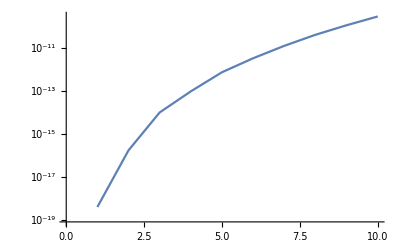

```mathematica
ListLogPlot[Ens, Joined->True]
```

```mathematica
DeltaFPlus[τ,γ,β]
```

(2 c ⅇ^(-ⅈ β) τ^γ (γ-ⅈ (1+γ) τ))/(1+2 γ)

```mathematica
4 c^2 τ^(2 γ) (γ^2 + τ^2 (γ+1)^2)/(2 γ+1)^2
```

(4 c^2 τ^(2 γ) (γ^2+(1+γ)^2 τ^2))/(1+2 γ)^2

```mathematica
CPPlus[τ,γ,β]
```

ⅇ^(ⅈ β) (γ (1+ⅈ τ) τ^(-1+γ)+ⅈ τ^γ)

```mathematica
τ^(γ-1)Sqrt[γ^2+(1+γ)^2 τ^2]4 c^2 τ^(2 γ) (γ^2 + τ^2 (γ+1)^2)/(2 γ+1)^2
```

(4 c^2 τ^(-1+3 γ) (γ^2+(1+γ)^2 τ^2)^(3/2))/(1+2 γ)^2

```mathematica
FF[γ_]:=Evaluate[Assuming[{γ>0, γ <1},8/(1+2 γ)^2 Integrate[ τ^(-1+3 γ) (γ^2+(1+γ)^2 τ^2)^(3/2),{τ,0,Tan[Pi γ/2]}]]]
```

```mathematica
ClearAll[F];
```

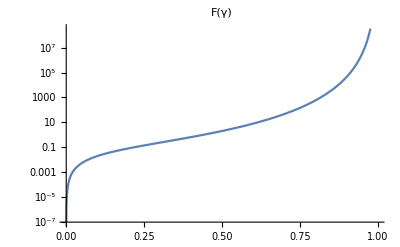

```mathematica
LogPlot[FF[γ],{γ,0.,1},PlotLabel->F[γ]]
```

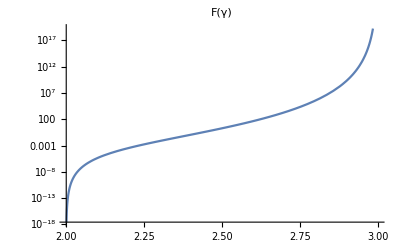

```mathematica
LogPlot[FF[γ],{γ,2.,3},PlotLabel->F[γ]]
```